# Gaining a better understanding of how to use Mathematica for physics

Peter Cullen Burbery

I have decided I am going to gain a better understanding of how to use Mathematica for physics and dimensional analysis. I started solving some problems from the American Association of Physics Teacher 2011 F=ma exam and I realized that I'm not taking full advantage of the functionality in Mathematica so  I decided to create a new essay where I work on just using Mathematica and working through the documentation.

## Plan

I will be working through the Units&Quantities guide.

I will be using the SI as defined in the BIPM's SI brochure which came into effect on 20 May 2019 after the CGPM voted to redefine the SI in terms of physical constants in 2018 at the Palace of Versailles.

I will also be using the copy of the SI Brochure published by NIST.

I will also not be using the prefixes that are not powers of 10. There are four of them but I'm not going to mention them being I'm trying to phase them out.

I will also be using the proposed prefixes ronna, ronto, quecto and quetta that the CGPM will vote on in November. Hopefully they add ronna for 27, quetta for 30, ronto for -27 and quecto for -30.

I would also like to mention that time is not completely redefined. Time will be probably be redefined in 2035. The other six defining constants are set in stone.

## Unit and Quantity Input

## Quantity

I will work through the properties and relations section for Quantity.

```mathematica
Quantity[1,"Webers"]
```

1 Wb

```mathematica
Quantity[1.7,"Henries""Webers"/"Teslas"]
```

1.7 H Wb/T

```mathematica
Quantity[1.7,"Siemens"("Becquerels")^2/("Katals")^3]
```

1.7 Bq^2 S/kat^3

I can define an IndependentUnit:

```mathematica
Quantity[7,IndependentUnit["donuts"]]
```

7 donuts

I'm thinking of the topology of donuts and coffee cups where a donut is the same as a coffee cup as well as a torus:

```mathematica
Quantity[7,IndependentUnit["donuts"]IndependentUnit["coffeecups"]/IndependentUnit["toruses"]^2]
```

7 coffeecups donuts/toruses^2

Add prefixes:

```mathematica
Quantity[1.7,"Ronnameters"]
```

1.7 Rm

```mathematica
Quantity[3.9,"Rontokelvins"]
```

3.9 r K

```mathematica
Quantity[3.9,"Rontowebers"]
```

3.9 r Wb

I wonder if I can combine an SI prefix with a non SI unit that is accepted for use with the SI?

```mathematica
Quantity[3.9,"Yottaminute"]
```

3.9 Y min

Yes I can. That's cool.

In its one argument form Quantity automatically sets the magnitude to 1:

```mathematica
Quantity["Sieverts"]
```

1 Sv

```mathematica
Quantity["Grays"]
```

1 Gy

Quantity will accept Quantity arguments:

```mathematica
Quantity[Quantity["Farads"],("Seconds")^-1]
```

1 F/s

```mathematica
Quantity[Quantity["Henries"],IndependentUnit["oranges"]]
```

1 H oranges

```mathematica
Quantity[Quantity["Henries"],IndependentUnit["apples"]]
```

1 H apples

Addition of Quantity objects will use heuristics:

```mathematica
qb=Quantity[1,"Teslas"];
qc=Quantity[100,"Gauss"];
CompatibleUnitQ[qb,qc]
```

True

```mathematica
qb+qc
```

10100 G

Products also use heuristics:

```mathematica
qd=Quantity[1,"Kilometers"];
qf=Quantity[3000,"Meters"];
CompatibleUnitQ[qd,qf]
```

True

```mathematica
qd*qf
```

3 km^2

Quantity threads over lists:

```mathematica
Quantity[{1,2,3,{4,5,{6}}},"Hertz"]
```

{1 Hz,2 Hz,3 Hz,{4 Hz,5 Hz,{6 Hz}}}

I noticed that QuantityArraypaclet:ref/QuantityArray[mags,units] would correspond to Quantitypaclet:ref/Quantity[mags,Threaded[units]] if Quantitypaclet:ref/Quantity had the Listablepaclet:ref/Listable attribute, and I think this change should be made where Quantity has the attribute Listable.

Canonical unit strings are always plural. Unit descriptions will accurately reflect the singular form of a unit:

```mathematica
Quantity[1,"Webers"]
```

1 Wb

```mathematica
%//InputForm
```

Quantity[1, "Webers"]

```mathematica
Quantity[1,"Webers"]//ToString
```

1 weber

Since Quantitypaclet:ref/Quantity is HoldRestpaclet:ref/HoldRest, it can accept multiple unit strings of the same dimension:

```mathematica
Quantity[3.5,"Yottameters"/"Ronnameters"]
```

3.5 Ym/Rm

```mathematica
Quantity[12,"Zettagrams"/"Yottagrams"]
```

12 Zg/Yg

When quantities are multiplied, the resulting unit is not automatically simplified:

```mathematica
qg=Quantity[1,"Newtons"];
qh=Quantity[10,"Meters"];
qg*qh
```

10 m N

Use UnitSimplifypaclet:ref/UnitSimplify to get a simpler form of the unit:

```mathematica
UnitSimplify[%]
```

10 J

Use UnitConvertpaclet:ref/UnitConvert to normalize mixed Quantitypaclet:ref/Quantity expressions to non-mixed Quantitypaclet:ref/Quantity expressions:

```mathematica
q=Quantity[MixedMagnitude[Range[24,0,-3]],MixedUnit[{"Yottaseconds","Zettaseconds","Exaseconds","Petaseconds","Teraseconds","Gigaseconds","Megaseconds","Kiloseconds","Seconds"}]]
```

24 Ys21 Zs18 Es15 Ps12 Ts9 Gs6 Ms3 ks0 s yottaseconds,zettaseconds,exaseconds,petaseconds,teraseconds,gigaseconds,megaseconds,kiloseconds,seconds

```mathematica
UnitConvert[q]
```

24021018015012009006003000 s

```mathematica
UnitConvert[q,"Minutes"]
```

400350300250200150100050 min

## QuantityArray

A QuantityArraypaclet:ref/QuantityArray object is interpreted as an array of Quantitypaclet:ref/Quantity objects:

```mathematica
qJ=QuantityArray[RandomReal[1,{20,2}],{"Meters","Seconds"}]
```

QuantityArray[…]

It is an array:

```mathematica
ArrayQ[qJ]
```

True

It is a list of pairs; hence, a matrix, not a vector:

```mathematica
MatrixQ[qJ]
```

True

```mathematica
VectorQ[qJ]
```

False

It is an array of Quantitypaclet:ref/Quantity objects, not an array of numbers:

```mathematica
MatrixQ[qJ,QuantityQ]
```

True

```mathematica
MatrixQ[qJ,NumericQ]
```

False

The QuantityArraypaclet:ref/QuantityArray representation is memory efficient:

```mathematica
qK=QuantityArray[RandomReal[1,{100,100,2}],{"Meters","Seconds"}]
```

QuantityArray[…]

```mathematica
nqK=Normal[qa,QuantityArray];
```

It uses only 6% of the memory of the corresponding normal representation:

```mathematica
ByteCount[qK]/ByteCount[nqK]//N
```

0.0590101

It also allows faster extraction of magnitudes and units:

```mathematica
QuantityMagnitude[qK];//AbsoluteTiming
```

{0.0002009,Null}

```mathematica
QuantityUnit[qJ];//AbsoluteTiming
```

{0.000391,Null}

Compare to the slower extraction from the normal array of quantities:

```mathematica
QuantityMagnitude[nqK];//AbsoluteTiming
```

{0.260329,Null}

```mathematica
QuantityUnit[nqK];//AbsoluteTiming
```

{0.403643,Null}

A single quantity is automatically converted into a Quantitypaclet:ref/Quantity object:

```mathematica
QuantityArray[7,"Meters"]
```

7 m

```mathematica
%//InputForm
```

Quantity[7, "Meters"]

This is a list with one quantity:

```mathematica
QuantityArray[{7},"Meters"]
```

QuantityArray[…]

```mathematica
%//Normal
```

{7 m}

It can also be given as:

```mathematica
QuantityArray[{7},{"Meters"}]
```

QuantityArray[…]

```mathematica
%//Normal
```

{7 m}

During conversion, QuantityArraypaclet:ref/QuantityArray does not try to change units:

```mathematica
QuantityArray[{Quantity[1,"Meters"],Quantity[2,"Zettameters"]}]
```

QuantityArray[…]

UnitConvertpaclet:ref/UnitConvert will unify the units:

```mathematica
UnitConvert[%,"Meters"]
```

QuantityArray[…]

```mathematica
Normal[%]
```

{1 m,2000000000000000000000 m}

The QuantityArraypaclet:ref/QuantityArray structure is preserved in multiple operations. Take two arrays:

```mathematica
qL=QuantityArray[{{1,20},{3,40},{5,60},{7,50}},{"Meters","Seconds"}]
```

QuantityArray[…]

```mathematica
qM=QuantityArray[{{10,2},{20,2},{30,2},{40,2}},{"Zettameters","Zettaseconds"}]
```

QuantityArray[…]

Addition of QuantityArraypaclet:ref/QuantityArray objects of compatible units, automatically converting some of them:

```mathematica
qL+qM
```

QuantityArray[…]

Multiplication of QuantityArraypaclet:ref/QuantityArray objects of compatible dimensions:

```mathematica
qL qM
```

QuantityArray[…]

Tensor product of QuantityArraypaclet:ref/QuantityArray objects:

```mathematica
TensorProduct[qL,qM]
```

QuantityArray[…]

Transposition is special because it stores the permutation:

```mathematica
Transpose[qL]
```

QuantityArray[…]

```mathematica
%//InputForm
```

QuantityArray[StructuredArray`StructuredData[{2, 4}, 
  {{{1, 20}, {3, 40}, {5, 60}, {7, 50}}, 
   {"Meters", "Seconds"}, {{2}, {1}}}]]

Flattening is also special in that sense:

```mathematica
Flatten[qL]
```

QuantityArray[…]

```mathematica
%//InputForm
```

QuantityArray[StructuredArray`StructuredData[{8}, 
  {{{1, 20}, {3, 40}, {5, 60}, {7, 50}}, 
   {"Meters", "Seconds"}, {{1, 2}}}]]

Partition the array:

```mathematica
Partition[qL,2]
```

QuantityArray[…]

```mathematica
%//InputForm
```

QuantityArray[StructuredArray`StructuredData[{2, 2, 2}, 
  {{{{1, 20}, {3, 40}}, {{5, 60}, {7, 50}}}, 
   {"Meters", "Seconds"}, {{1}, {2}, {3}}}]]

Flatten it again:

```mathematica
Flatten[%%,1]
```

QuantityArray[…]

The result is an equivalent representation of the original quantity array:

```mathematica
%==qL
```

True

Take a QuantityArraypaclet:ref/QuantityArray object with compatible but different units:

```mathematica
qN=QuantityArray[{{1,2},{3,4},{5,6}},{"Meters","Yottameters"}]
```

QuantityArray[…]

CommonUnitspaclet:ref/CommonUnits will convert it into a single unit array:

```mathematica
CommonUnits[qN]
```

QuantityArray[…]

```mathematica
Normal[%]
```

{{1 m,2000000000000000000000000 m},{3 m,4000000000000000000000000 m},{5 m,6000000000000000000000000 m}}

To select the unit, use UnitConvertpaclet:ref/UnitConvert:

```mathematica
UnitConvert[qN,"Meters"]
```

QuantityArray[…]

```mathematica
Normal[%]
```

{{1 m,2000000000000000000000000 m},{3 m,4000000000000000000000000 m},{5 m,6000000000000000000000000 m}}

A QuantityArraypaclet:ref/QuantityArray object of infinite precision:

```mathematica
qP=QuantityArray[{{1,2},{3,4}},{"Meters","Seconds"}]
```

QuantityArray[…]

```mathematica
Precision[qP]
```

∞

Numericize to precision 20:

```mathematica
nqP=N[qP,20]
```

QuantityArray[…]

```mathematica
Precision[nqP]
```

20.

```mathematica
InputForm[nqP]
```

QuantityArray[StructuredArray`StructuredData[{2, 2}, 
  {{{1.`20., 2.`20.}, {3.`20., 4.`20.}}, 
   {"Meters", "Seconds"}, {{1}, {2}}}]]

The arithmetic operations take precision into account:

```mathematica
Precision[2. qP]
```

MachinePrecision

QuantityArraypaclet:ref/QuantityArray will automatically attempt to interpret an unknown unit string:

```mathematica
QuantityArray[RandomReal[1,10],"m"]
```

QuantityArray[…]

```mathematica
QuantityArray[{{1,20},{3,40},{5,60},{7,50}},{"m s^-1","V/A"}]
```

QuantityArray[…]

Possible Issues

Normalization of QuantityArraypaclet:ref/QuantityArray objects also normalizes purely numerical quantities such as percents:

```mathematica
qQ=QuantityArray[{10,30,79},"Percent"]
```

QuantityArray[…]

```mathematica
Normal[qQ]
```

{1/10,3/10,79/100}

Specify that only the QuantityArraypaclet:ref/QuantityArray structure should be normalized:

```mathematica
Normal[qQ,QuantityArray]
```

{10 %,30 %,79 %}

In details it mentions SparseArray is supported.

```mathematica
SparseArray[Thread[Table[{k,k},{k,1000}]->Prime[Range[1000]]]]
```

SparseArray[…]

```mathematica
QuantityArray[SparseArray[Thread[Table[{k,k},{k,1000}]->Prime[Range[1000]]]],"Meters"]
```

QuantityArray[…]

```mathematica
ByteCount[QuantityArray[SparseArray[Thread[Table[{k,k},{k,1000}]->Prime[Range[1000]]]],"Meters"]]
```

25632

Find the determinant:

```mathematica
Det[QuantityArray[SparseArray[Thread[Table[{k,k},{k,1000}]->Prime[Range[1000]]]],"Meters"]]
```

678629608419755514953266004896957820972161078160377361970324401521111792080121479864721936071815069425907219215791646774510151130705671056416094404541167439287735488353736963531288441938981088407654256240451529081607242659988552012480001287133802278572298314458227654950008738955663072953766341488209509227159933381319371567666804963833249523370831655778314080604712246344649628072459805028063160913071005795183295590443375991860551286230065601580359306757988823124262933259305966372664091680948986620887898883461227980556352852601733860114246410887151983493540958775872577571329277597701163671587052591794386970584444752423596023268793021595936555282977008138833858707329536639661377014042325817639809356799596347944462538427778375525904007169834445567450156949173690701738594584875536885957881452438269676946038980597530032671949818526703398270502591574889228837327819994695664173214894557366363343168494592437205324652573516528943874382178600874878024643322031797588414862315122048846223291257900756812820806739795819803783834366449110996030165071920678407750230118672657378102915524688059208755108467225277065866103666795739208709483959119145497860116133180335757702319385020561042517429031288526721801002679092058170909635701703382390753126302005323612316630558515594616479515096004453718500060291836932140612551722161051067379805065002788004096547708243964735215852734827632098700684466036892770059458754742495711074949314613079781545359495019757827538184361308856825999513366660884541936335491466045305322353749545362962683762333460252556042583248154845846566948014188971651057314058851019340282646752239847232045463969939303431371658607220786663205842510175297602195433569758123945251755043878718459161595137019904240640962465899496512410906852088532419874383895656303779315512987369934711061777117329635461569528504994783413643047392160871963795694958724055597996525917454740621526108635321204763824742430011606570436994644169759611263012712375861911682673548369764923418748711813157811279361700331599397588282864147719911156923709896847720603482450047076226728760035577410722701184878333100234780537897462936378382079055966277885316116887834607362114802378706815302650083359076798475953780285866955566883261644281750278358349579977889429105626865087038835977930842352223971442123281019745568694318200865586150762549114357677130353514342849892002965601064686292493671204318349298134598116662388818407027989992498970986262856712232401426575229549744739851333516937170071337085705197690437625282926914858257689908846227286051735284322402597283976180484905838486513162987381659809287870592690902387482033879184700359561190209417618607868793293476867624464497838299321267571049753373623085351455438610076341961842557148160442782839736179329056237366708383637405663196770746783100179128651460773512143616414356080816160456447832856222804164147618891013658880373227849181446498052320436905124576367614898030410445386643656246089772967461562154147355201124738052009172637452710027640262529821855681129322547617443299372089380860873141895162966481252930360380537684913059090577224188204179681342669502124011214018434733385892140553307905100266308832521127607403573729242486985024795253305646999864066282626291530104297235324933472771821035277094700384260778312268190937365143307612108901729316774669077441981239149913617114331308200242717771235228048768133852203532299832810943137983635951570 m^1000

Retrieve the timing:

```mathematica
Det[QuantityArray[SparseArray[Thread[Table[{k,k},{k,1000}]->Prime[Range[1000]]]],"Meters"]]//RepeatedTiming
```

{0.851515,678629608419755514953266004896957820972161078160377361970324401521111792080121479864721936071815069425907219215791646774510151130705671056416094404541167439287735488353736963531288441938981088407654256240451529081607242659988552012480001287133802278572298314458227654950008738955663072953766341488209509227159933381319371567666804963833249523370831655778314080604712246344649628072459805028063160913071005795183295590443375991860551286230065601580359306757988823124262933259305966372664091680948986620887898883461227980556352852601733860114246410887151983493540958775872577571329277597701163671587052591794386970584444752423596023268793021595936555282977008138833858707329536639661377014042325817639809356799596347944462538427778375525904007169834445567450156949173690701738594584875536885957881452438269676946038980597530032671949818526703398270502591574889228837327819994695664173214894557366363343168494592437205324652573516528943874382178600874878024643322031797588414862315122048846223291257900756812820806739795819803783834366449110996030165071920678407750230118672657378102915524688059208755108467225277065866103666795739208709483959119145497860116133180335757702319385020561042517429031288526721801002679092058170909635701703382390753126302005323612316630558515594616479515096004453718500060291836932140612551722161051067379805065002788004096547708243964735215852734827632098700684466036892770059458754742495711074949314613079781545359495019757827538184361308856825999513366660884541936335491466045305322353749545362962683762333460252556042583248154845846566948014188971651057314058851019340282646752239847232045463969939303431371658607220786663205842510175297602195433569758123945251755043878718459161595137019904240640962465899496512410906852088532419874383895656303779315512987369934711061777117329635461569528504994783413643047392160871963795694958724055597996525917454740621526108635321204763824742430011606570436994644169759611263012712375861911682673548369764923418748711813157811279361700331599397588282864147719911156923709896847720603482450047076226728760035577410722701184878333100234780537897462936378382079055966277885316116887834607362114802378706815302650083359076798475953780285866955566883261644281750278358349579977889429105626865087038835977930842352223971442123281019745568694318200865586150762549114357677130353514342849892002965601064686292493671204318349298134598116662388818407027989992498970986262856712232401426575229549744739851333516937170071337085705197690437625282926914858257689908846227286051735284322402597283976180484905838486513162987381659809287870592690902387482033879184700359561190209417618607868793293476867624464497838299321267571049753373623085351455438610076341961842557148160442782839736179329056237366708383637405663196770746783100179128651460773512143616414356080816160456447832856222804164147618891013658880373227849181446498052320436905124576367614898030410445386643656246089772967461562154147355201124738052009172637452710027640262529821855681129322547617443299372089380860873141895162966481252930360380537684913059090577224188204179681342669502124011214018434733385892140553307905100266308832521127607403573729242486985024795253305646999864066282626291530104297235324933472771821035277094700384260778312268190937365143307612108901729316774669077441981239149913617114331308200242717771235228048768133852203532299832810943137983635951570 m^1000}

## QuantityDistribution

QuantityDistributionpaclet:ref/QuantityDistribution with dimensionless units will auto-evaluate to the magnitude distribution:

```mathematica
QuantityDistribution[GammaDistribution[2,3],"DimensionlessUnit"]
```

GammaDistribution[2,3]

```mathematica
QuantityDistribution[GammaDistribution[2,3],"Meters"/"Meters"]
```

GammaDistribution[2,3]

Use QuantityMagnitudepaclet:ref/QuantityMagnitude and QuantityUnitpaclet:ref/QuantityUnit to extract distribution and units:

```mathematica
qdist=NormalDistribution[Quantity[120, "Petameters"],Quantity[16, "Petameters"]]
```

QuantityDistribution[NormalDistribution[120,16], Pm]

```mathematica
{QuantityMagnitude[qdist],QuantityUnit[qdist]}
```

{NormalDistribution[120,16],Petameters}

QuantityDistributionpaclet:ref/QuantityDistribution[dist,unit] is equivalent to TransformedDistributionpaclet:ref/TransformedDistribution:

```mathematica
TransformedDistribution[Quantity[x,"Sieverts"],x\[Distributed]NormalDistribution[μ,σ]]
```

QuantityDistribution[NormalDistribution[μ,σ], Sv]

Skewness and kurtosis of a QuantityDistributionpaclet:ref/QuantityDistribution are unitless:

```mathematica
𝒟=QuantityDistribution[GumbelDistribution[20,3],"Watts"];
```

```mathematica
Skewness[𝒟]
```

-(12 √6 Zeta[3])/π^3

```mathematica
Kurtosis[𝒟]
```

27/5

Joint distribution of mass and acceleration:

```mathematica
𝒟=QuantityDistribution[BinormalDistribution[{200,9.81},{5,0.01},1/2],{"Grams","Meters"/"Seconds"^2}];
```

The unit of the moment of order (1,1) is the product of units of each component:

```mathematica
Moment[𝒟,{1,1}]
```

1962.03 g m/s^2

The moment can be interpreted as the expected value of force:

```mathematica
UnitSimplify[%]
```

1.96203 N

PDFpaclet:ref/PDF of a continuous distribution with units integrates to 1 over its domain:

```mathematica
𝒟=CauchyDistribution[Quantity[120, "Petameters"],Quantity[16, "Petameters"]]
```

QuantityDistribution[CauchyDistribution[120,16], Pm]

```mathematica
pdf=PDF[𝒟,Quantity[x,"Meters"]]
```

1/(16 π (1+1/256 (-120+x/1000000000000000)^2)) /Pm

Reciprocal units of the density function are canceled by the unit of the measure to give unitless antiderivative:

```mathematica
Integrate[pdf,Quantity[x,"Petameters"]]
```

-(1000000000000000 ArcTan[1/16 (120-x/1000000000000000)])/π

Total probability is equal to 1:

```mathematica
Integrate[pdf,{Quantity[x,"Meters"],Quantity[-∞, "Meters"],Quantity[+∞, "Meters"]}]
```

1

This is the start of the section on Possible Issues.

The dimensionality of the distribution and units must agree:

```mathematica
𝒟=QuantityDistribution[BinormalDistribution[r],{"Meters","Hertz","Watts"}];
DistributionParameterQ[𝒟]
```

False

Specify two units for two dimensions:

```mathematica
𝒟=QuantityDistribution[BinormalDistribution[r],{"Meters","Teslas"}];
Mean[𝒟]
```

{0 m,0 T}

The identical unit for all dimensions:

```mathematica
𝒟=QuantityDistribution[BinormalDistribution[r],"Volts"];
Mean[𝒟]
```

{0 V,0 V}

The unit conversion may map the data outside of the support of the distribution:

```mathematica
data=QuantityArray[RandomVariate[MultinomialDistribution[15,{.3,.7}],100],{"Grams","Teragrams"}];
```

Estimate a quantity distribution in kilograms:

```mathematica
EstimatedDistribution[data,QuantityDistribution[MultinomialDistribution[n,{p,q}],"Kilograms"]]
```

EstimatedDistribution[QuantityArray[…],QuantityDistribution[MultinomialDistribution[n,{p,q}], kg]]

Estimate using the units of the data:

```mathematica
EstimatedDistribution[data,MultinomialDistribution[n,{p,q}]]
```

QuantityDistribution[MultinomialDistribution[15,{0.301333,0.698667}],{ g, Tg}]

Then convert the distribution:

```mathematica
UnitConvert[%,"Kilograms"]
```

QuantityDistribution[TransformedDistribution[{x1/1000,1000000000 x2},{x1,x2}\[Distributed]MultinomialDistribution[15,{0.301333,0.698667}]], kg]

Setting fixed values for parameter estimation is unit dependent:

```mathematica
data=QuantityArray[RandomReal[{-1,1},10^2],"DegreesCelsius"]
```

QuantityArray[…]

```mathematica
distC=EstimatedDistribution[data,NormalDistribution[0,s]]
```

QuantityDistribution[NormalDistribution[0,0.54868], °C]

```mathematica
distK=EstimatedDistribution[UnitConvert[data,"DegreesKelvin"],NormalDistribution[0,s]]
```

QuantityDistribution[NormalDistribution[0,273.067], K]

Compare standard deviations:

```mathematica
{StandardDeviation[distC],UnitConvert[StandardDeviation[distK],"DegreesCelsius"]}
```

{0.54868 °C,-0.0831211 °C}

This is caused by:

```mathematica
{QuantityMagnitude[Quantity[0,"DegreesCelsius"]],QuantityMagnitude[Quantity[0,"DegreesFahrenheit"],"DegreesCelsius"]}
```

{0,-160/9}

Convert the whole quantity distribution instead:

```mathematica
UnitConvert[distK,"DegreesCelsius"]
```

QuantityDistribution[NormalDistribution[-5463/20,273.067], °C]

Use converted units in call to estimation:

```mathematica
distK2=EstimatedDistribution[UnitConvert[data,"DegreesKelvin"],NormalDistribution[QuantityMagnitude[Quantity[0,"DegreesKelvin"],"DegreesKelvin"],s]]
```

QuantityDistribution[NormalDistribution[0,273.067], K]

```mathematica
UnitConvert[distK2,"DegreesCelsius"]
```

QuantityDistribution[NormalDistribution[-5463/20,273.067], °C]

```mathematica
%==distC
```

QuantityDistribution[NormalDistribution[-5463/20,273.067], °C]==QuantityDistribution[NormalDistribution[0,0.54868], °C]

Hmm this should be True but I changed Fahrenheit to Kelvin so I might have messed something up.

The magnitude of the factorial moment of a QuantityDistributionpaclet:ref/QuantityDistribution coincides with the factorial moment of the magnitude distribution:

```mathematica
𝒟=QuantityDistribution[NormalDistribution[μ,σ],"Meters"]
```

QuantityDistribution[NormalDistribution[μ,σ], m]

```mathematica
FactorialMoment[𝒟,2]
```

(-μ+μ^2+σ^2) m^2

```mathematica
FactorialMoment[NormalDistribution[μ,σ],2]
```

-μ+μ^2+σ^2

Factorial moment expression is not homogeneous in the location and scale parameters, hence direct substitution of quantity parameters results in an error:

```mathematica
%/.{μ->Quantity[μ,"Meters"],σ->Quantity[σ,"Meters"]}
```

-μ m^2+(μ^2+σ^2) m^4

The error is in the message box but doesn't display directly.

## Quantity Components

## QuantityMagnitude

```mathematica
QuantityMagnitude[{Quantity[3.2, "Meters"],Quantity[34, "Kilograms"]}]
```

{3.2,34}

```mathematica
QuantityMagnitude[{{Quantity[40, "Webers"],Quantity[100, "Siemens"]},Quantity[4, "Henries"]}]
```

{{40,100},4}

```mathematica
QuantityMagnitude[{Quantity[1, "Hours"],Quantity[1, "Seconds"]},{"Days","Weeks","Decades"}]
```

{{1/24,1/168,5/438291},{1/86400,1/604800,1/315569520}}

```mathematica
Quantity[MixedMagnitude[{1002,80}],MixedUnit[{"Meters","Kilometers"}]]
```

2 81

```mathematica
QuantityMagnitude[%]
```

MixedMagnitude[{2,81}]

## QuantityUnit

```mathematica
QuantityUnit[Quantity[50, "Megameters"]]
```

Megameters

## UnitDimensions

UnitDimensionspaclet:ref/UnitDimensions returns the base dimension of a unit:

```mathematica
UnitDimensions[Quantity[3,"Spins"]]
```

{{LengthUnit,2},{MassUnit,1},{TimeUnit,-1}}

```mathematica
UnitDimensions[Quantity[7000,"Henries"]]
```

{{ElectricCurrentUnit,-2},{LengthUnit,2},{MassUnit,1},{TimeUnit,-2}}

The dimension pairs are returned lexically ordered:

```mathematica
UnitDimensions[Quantity[5,"Meters"*"Seconds"]]
```

{{LengthUnit,1},{TimeUnit,1}}

```mathematica
UnitDimensions[Quantity[5,"Seconds"*"Meters"]]
```

{{LengthUnit,1},{TimeUnit,1}}

UnitDimensionspaclet:ref/UnitDimensions returns the argument of an IndependentUnitpaclet:ref/IndependentUnit specification together with its power:

```mathematica
Quantity[3,"Kilometers"*IndependentUnit["myUnit"]^2]
```

3 km myUnit^2

```mathematica
UnitDimensions[%]
```

{{LengthUnit,1},{IndependentUnitDimension[myUnit],2}}

UnitDimensionspaclet:ref/UnitDimensions returns one dimension pair for a MixedUnitpaclet:ref/MixedUnit specification:

```mathematica
Quantity[MixedMagnitude[{5,10}],MixedUnit[{"Megameters","Meters"}]]
```

5 10

```mathematica
UnitDimensions[%]
```

{{LengthUnit,1}}

UnitDimensionspaclet:ref/UnitDimensions ignores the date in DatedUnitpaclet:ref/DatedUnit specifications:

```mathematica
UnitDimensions[DatedUnit["Meters",1889]]
```

{{LengthUnit,1}}

```mathematica
UnitDimensions[DatedUnit["USDollars",2000]]
```

{{MoneyUnit,1}}

An empty list is returned for units without dimension:

```mathematica
UnitDimensions[Quantity[72,"Percent"]]
```

{}

```mathematica
UnitDimensions[Quantity[98,"Scores"]]
```

{}

A unit given as a prefix only is dimensionless:

```mathematica
UnitDimensions[Quantity[100000,"Gigameters"]]
```

{{LengthUnit,1}}

```mathematica
UnitDimensions[Quantity[100,"Giga"]]
```

{}

UnitDimensionspaclet:ref/UnitDimensions will automatically attempt to interpret an unknown unit string:

```mathematica
KnownUnitQ["OddCandle"]
```

False

```mathematica
(*my example*)UnitDimensions["OddCandle"]
```

Quantity::unkunit: Unable to interpret unit specification OddCandle.

UnitDimensions[OddCandle]

```mathematica
(*my example*) KnownUnitQ["OldCandle"]
```

False

This documentation needs to be updated. The output I copied originally was

```mathematica
(*Documentation example*) UnitDimensions["OddCandle"]
```

{{LuminousIntensityUnit,1}}

```mathematica
(*Documentation example*) KnownUnitQ["OldCandle"]
```

True

This doesn't match the error that OddCandle could not be interpreted above.

UnitDimensionspaclet:ref/UnitDimensions threads over lists:

```mathematica
UnitDimensions[{Quantity[7, "Meters"],Quantity[8, "Bits"],Quantity[5, "Megagrams"]}]
```

{{{LengthUnit,1}},{{InformationUnit,1}},{{MassUnit,1}}}

```mathematica
UnitDimensions[{Quantity[7, "Minutes"],{Quantity[2, "Radians"]},Quantity[5, "Steradians"]}]
```

{{{TimeUnit,1}},{{{AngleUnit,1}}},{{AngleUnit,2}}}

Numerical values are considered dimensionless:

```mathematica
UnitDimensions[Pi]
```

{}

## QuantityQ

QuantityQpaclet:ref/QuantityQ returns Falsepaclet:ref/False for any expression whose head is not Quantitypaclet:ref/Quantity:

```mathematica
QuantityQ[2]
```

False

```mathematica
QuantityQ[x]
```

False

```mathematica
QuantityQ[{Quantity[7, "Weeks"],Quantity[2, "Hours"]}]
```

False

In particular, QuantityArraypaclet:ref/QuantityArray, QuantityVariablepaclet:ref/QuantityVariable, and QuantityDistributionpaclet:ref/QuantityDistribution are not QuantityQpaclet:ref/QuantityQ objects:

```mathematica
QuantityQ[QuantityArray[{2.3,1.5,9.0},"Meters"]]
```

False

```mathematica
QuantityQ[QuantityVariable["V","ElectricPotential"]]
```

False

```mathematica
QuantityQ[QuantityDistribution[NormalDistribution[12,6],Quantity[, "Centimeters"]]]
```

False

QuantityQpaclet:ref/QuantityQ returns Falsepaclet:ref/False for Quantitypaclet:ref/Quantity expressions with invalid arguments:

```mathematica
Quantity[2,x]
```

Quantity[2,x]

```mathematica
QuantityQ[%]
```

False

```mathematica
Quantity[2,Quantity["Meters"]]
```

Quantity[2,1 m]

```mathematica
QuantityQ[%]
```

False

QuantityQpaclet:ref/QuantityQ returns Truepaclet:ref/True only for Quantitypaclet:ref/Quantity expressions with valid arguments:

```mathematica
Quantity[2,"Meters"]
```

2 m

```mathematica
QuantityQ[%]
```

True

```mathematica
Quantity[2,IndependentUnit["myUnit"]^3]
```

2 myUnit^3

```mathematica
QuantityQ[%]
```

True

```mathematica
Quantity[MixedMagnitude[{5,10}],
MixedUnit[{"Meter","Millimeters"}]]
```

5 10

```mathematica
QuantityQ[%]
```

True

## KnownUnitQ

I will now focus on the Scope section instead of the Properties & Relations section.

Units represented by a single string:

```mathematica
KnownUnitQ["Meters"]
```

True

```mathematica
KnownUnitQ["Siemens"]
```

True

Products of known units:

```mathematica
KnownUnitQ["Newtons"*"Meters"]
```

True

```mathematica
KnownUnitQ["Watts"/"Meters"^2]
```

True

KnownUnitQpaclet:ref/KnownUnitQ returns Truepaclet:ref/True for valid IndependentUnitpaclet:ref/IndependentUnit specifications:

```mathematica
KnownUnitQ[IndependentUnit["myUnit"]]
```

True

```mathematica
KnownUnitQ[IndependentUnit["Unit1"]/IndependentUnit["Unit2"]^3]
```

True

It returns Falsepaclet:ref/False for invalid IndependentUnitpaclet:ref/IndependentUnit specifications:

```mathematica
KnownUnitQ[IndependentUnit[1]]
```

False

```mathematica
KnownUnitQ[IndependentUnit[unit]]
```

False

MixedUnitpaclet:ref/MixedUnit specifications of compatible units:

```mathematica
KnownUnitQ[MixedUnit[{"Gigameters","Millimeters"}]]
```

True

Incompatible units do not produce a valid MixedUnitpaclet:ref/MixedUnit specification:

```mathematica
KnownUnitQ[MixedUnit[{"Seconds","Millimeters"}]]
```

False

DatedUnitpaclet:ref/DatedUnit specifications:

```mathematica
KnownUnitQ[DatedUnit["USDollars", 1990]]
```

True

```mathematica
KnownUnitQ[DatedUnit["Euros", Today]]
```

True

Prefixes are dimensionless known units:

```mathematica
KnownUnitQ["Centi"]
```

True

```mathematica
KnownUnitQ["Mega"]
```

True

This function be helpful for making a prefix table where regex would be used to test if a string is a valid unit for example μΩ is a valid symbol for the micro-ohm, but ηρ is not a valid symbol.

Numeric expressions are not canonical units:

```mathematica
KnownUnitQ[1]
```

False

```mathematica
KnownUnitQ[Sqrt[2]]
```

False

## Quantity Display

## QuantityForm

```mathematica
QuantityForm[Quantity[3,"Siemens"/("Meters")^3],"LongForm"]
```

3 siemens per meter cubed

QuantityFormpaclet:ref/QuantityForm acts on all Quantitypaclet:ref/Quantity objects in an expression:

```mathematica
QuantityForm[{Quantity[4, "Joules"],Quantity[9, "Sieverts"],Quantity[3, "Ohms"]},{"Abbreviation","LongForm"}]
```

{4 J(joules),9 Sv(sieverts),3 Ω(ohms)}

```mathematica
QuantityForm[<|"Distance"->Quantity[260, "Miles"],"Duration"->Quantity[3, "Hours"]|>,"LongForm"]
```

<|Distance→260 miles,Duration→3 hours|>

Possible display forms are "Abbreviation" and "LongForm":

```mathematica
expr=Quantity[5,"Grams"/"Meters"^3]
```

5 g/m^3

```mathematica
QuantityForm[expr,"Abbreviation"]
```

5 g/m^3

```mathematica
QuantityForm[expr,"LongForm"]
```

5 grams per meter cubed

"LongForm" descriptions will select singular/plural tenses based on the value of each Quantitypaclet:ref/Quantity:

```mathematica
QuantityForm[Quantity[1,"Seconds"],{"LongForm"}]
```

1 second

```mathematica
QuantityForm[Quantity[.7,"Seconds"],{"LongForm"}]
```

0.7 seconds

"SingularForm" can be used with "LongForm" to force unit descriptions to be in singular tense:

```mathematica
QuantityForm[Quantity[.7,"Seconds"],{"LongForm","SingularForm"}]
```

0.7 second

If the first argument is a canonical unit, QuantityFormpaclet:ref/QuantityForm will print with the specified form of the unit:

```mathematica
QuantityForm["Meters",{"Abbreviation","LongForm"}]
```

m(meters)

QuantityFormpaclet:ref/QuantityForm works with MixedUnitpaclet:ref/MixedUnit specifications:

```mathematica
Quantity[MixedMagnitude[{1,2}],MixedUnit[{"Exameters","Petameters"}]]
```

1 2

```mathematica
QuantityForm[%,{"Abbreviation","LongForm"}]
```

1 Em2 Pm(exameters,petameters)

## TargetUnits

TargetUnitspaclet:ref/TargetUnits can be used to specify which units to use in the visualization:

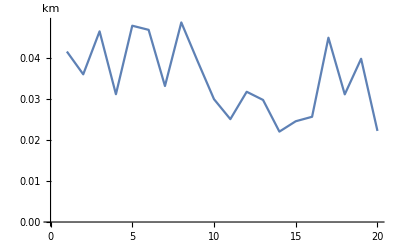

```mathematica
ListLinePlot[Quantity[RandomReal[{20,50},{20}],"Meters"],TargetUnits->"Kilometers",AxesLabel->Automatic]
```

TargetUnitspaclet:ref/TargetUnits can also be used to specify units for purely numerical data:

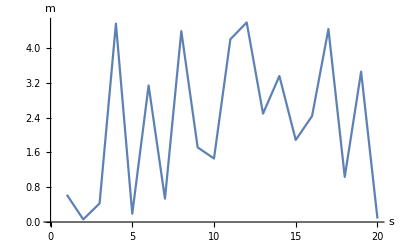

```mathematica
ListLinePlot[RandomReal[{0,5},{20}],TargetUnits->{"Seconds","Meters"},AxesLabel->Automatic]
```

## Unit Conversion

First I can set the unit system to metric.

```mathematica
$UnitSystem="Metric"
```

Metric

Verify Mathematica is using the metric system:

```mathematica
$UnitSystem
```

Metric

## UnitConvert

The first argument of UnitConvertpaclet:ref/UnitConvert can be given as a unit string:

```mathematica
UnitConvert["Grays"]
```

1 m^2/s^2

```mathematica
UnitConvert["Joules"]
```

1 kg m^2/s^2

The targetunit specification can be a product or quotient of strings:

```mathematica
UnitConvert[Quantity[1, "Joules"],"Newtons"*"Gigameters"]
```

1/1000000000 Gm N

```mathematica
UnitConvert[Quantity[1, ("Kilograms")/("Meters")^3],"Petagrams"/"Exameters"^3]
```

1000000000000000000000000000000000000000000 Pg/Em^3

An independent unit can only be converted to itself and multiples or submultiples of itself:

```mathematica
UnitConvert[Quantity[12, "Kilo" IndependentUnit["Stamps"]]]
```

12000 Stamps

```mathematica
UnitConvert[Quantity[1, "Mega" IndependentUnit["Coins"]],"Kilo"IndependentUnit["Coins"]]
```

1000 k Coins

I want to add my own example of oranges:

```mathematica
UnitConvert[Quantity[1, "Yotta" IndependentUnit["Oranges"]],"Zetta"IndependentUnit["Oranges"]]
```

1000 Z Oranges

```mathematica
UnitConvert[Quantity[1, "Tera" IndependentUnit["Apples"]],"Peta"IndependentUnit["Apples"]]
```

1/1000 P Apples

The second argument of UnitConvertpaclet:ref/UnitConvert can be a MixedUnitpaclet:ref/MixedUnit specification:

```mathematica
UnitConvert[Quantity[134963702,"Seconds"],
MixedUnit[{"Megaseconds","Kiloseconds","Seconds"}]]
```

134 963

The units given in a MixedUnitpaclet:ref/MixedUnit specification do not need to be ordered:

```mathematica
UnitConvert[Quantity[134963702,"Seconds"],
MixedUnit[{"Seconds","Kiloseconds","Megaseconds"}]]
```

702 963

UnitConvertpaclet:ref/UnitConvert can convert mixed Quantitypaclet:ref/Quantity objects:

```mathematica
Quantity[MixedMagnitude[{5,10}],MixedUnit[{"Petaseconds","Teraseconds"}]]
```

5 10

```mathematica
UnitConvert[%,MixedUnit[{"Gigaseconds","Seconds"}]]
```

5010000 0

UnitConvertpaclet:ref/UnitConvert will automatically attempt to interpret an unknown unit string:

```mathematica
KnownUnitQ["OddCandle"]
```

False

```mathematica
UnitConvert[Quantity[1, "Candelas"],"OddCandle"]
```

Quantity::unkunit: Unable to interpret unit specification OddCandle.

UnitConvert[1 cd,OddCandle]

The documentation has the following output which is different from my output with the interpretation error:

```mathematica
UnitConvert[Quantity[1, "Candelas"],"OddCandle"]
```

0.98 old candles

```mathematica
KnownUnitQ["OldCandle"]
```

True

When the target unit is specified as a Quantitypaclet:ref/Quantity object, its magnitude will be ignored:

```mathematica
UnitConvert[Quantity[1000, "Petameters"],"Meters"]
```

1000000000000000000 m

```mathematica
UnitConvert[Quantity[1000, "Petameters"],Quantity[1000, "Meters"]]
```

1000000000000000000 m

The "SIBase" unit for "InformationUnit" is "Bits":

```mathematica
UnitConvert[Quantity[16, "Gigaoctets"]]
```

128000000000 b

The "SIBase" unit for "MoneyUnit" is "USDollars":

```mathematica
UnitConvert[Quantity[100, "BritishPounds"]]
```

113.14 $

```mathematica
UnitConvert[Quantity["500.00", "Euros"]]
```

491.75 $

UnitConvertpaclet:ref/UnitConvert threads over lists:

```mathematica
UnitConvert[{Quantity[7, "Minutes"],Quantity[9, "Daltons"],Quantity[150, "PlanckLength"]}]
```

{420 s,1.49448516×10^-26 kg,2.424×10^-33 m}

## CompatibleUnitQ

CompatibleUnitQpaclet:ref/CompatibleUnitQ returns Truepaclet:ref/True when its elements have the same UnitDimensionspaclet:ref/UnitDimensions:

```mathematica
CompatibleUnitQ[Quantity[10, "Meters"],Quantity[1, "Kilometers"]]
```

True

```mathematica
UnitDimensions/@{Quantity[10, "Meters"],Quantity[1, "Kilometers"]}
```

{{{LengthUnit,1}},{{LengthUnit,1}}}

An IndependentUnitpaclet:ref/IndependentUnit object is only compatible with itself:

```mathematica
CompatibleUnitQ[IndependentUnit["donuts"],IndependentUnit["donuts"]]
```

True

```mathematica
CompatibleUnitQ[Quantity[3,IndependentUnit["donuts"]],Quantity[-2,"Nano"IndependentUnit["donuts"]]]
```

True

Known units are not compatible with IndependentUnitpaclet:ref/IndependentUnit objects of the same name:

```mathematica
CompatibleUnitQ["Meters",IndependentUnit["Meters"]]
```

False

Numeric expressions are treated as dimensionless quantities:

```mathematica
CompatibleUnitQ[Quantity[50,"Percent"],π]
```

True

CompatibleUnitQpaclet:ref/CompatibleUnitQ will automatically attempt to interpret an unknown unit string:

```mathematica
KnownUnitQ["Henryes"]
```

False

```mathematica
CompatibleUnitQ["Seconds"/"Siemens","Henryes"]
```

True

```mathematica
KnownUnitQ["Henries"]
```

True

CompatibleUnitQpaclet:ref/CompatibleUnitQ with one argument is similar to KnownUnitQpaclet:ref/KnownUnitQ:

```mathematica
{CompatibleUnitQ["Meters"],KnownUnitQ["Meters"]}
```

{True,True}

CompatibleUnitQpaclet:ref/CompatibleUnitQ accepts numeric expressions:

```mathematica
{CompatibleUnitQ[3],KnownUnitQ[3]}
```

{True,False}

CompatibleUnitQpaclet:ref/CompatibleUnitQ attempts to interpret unknown unit strings:

```mathematica
{CompatibleUnitQ["second"],KnownUnitQ["second"]}
```

{True,False}

If elements other than quantities and units are present, CompatibleUnitQpaclet:ref/CompatibleUnitQ returns Falsepaclet:ref/False:

```mathematica
CompatibleUnitQ[Quantity[1,"Watts"],x]
```

False

```mathematica
CompatibleUnitQ[x]
```

False

## CommonUnits

CommonUnitspaclet:ref/CommonUnits converts quantities sharing the same UnitDimensionspaclet:ref/UnitDimensions:

```mathematica
CommonUnits[{Quantity[0.5, "Teslas"],Quantity[200, "Gausses"],Quantity[1000, ("Webers")/("Megameters")^2]}]
```

{5000. G,200 G,1/100000 G}

```mathematica
UnitDimensions/@{Quantity[0.5, "Teslas"],Quantity[200, "Gausses"],Quantity[1000, ("Webers")/("Megameters")^2]}
```

{{{ElectricCurrentUnit,-1},{MassUnit,1},{TimeUnit,-2}},{{ElectricCurrentUnit,-1},{MassUnit,1},{TimeUnit,-2}},{{ElectricCurrentUnit,-1},{MassUnit,1},{TimeUnit,-2}}}

CommonUnitspaclet:ref/CommonUnits acts on subsets of quantities sharing the same UnitDimensionspaclet:ref/UnitDimensions:

```mathematica
CommonUnits[{Quantity[3., ("Meters")/("Seconds")],Quantity[0.23, "Kilograms"],Quantity[, "SpeedOfLight"],Quantity[, "PlanckMass"]}]
```

{1.00069×10^-8 c,230. g, c,0.00002176 g}

```mathematica
GroupBy[{Quantity[3., ("Meters")/("Seconds")],Quantity[0.23, "Kilograms"],Quantity[, "SpeedOfLight"],Quantity[, "PlanckMass"]},UnitDimensions]
```

<|{{LengthUnit,1},{TimeUnit,-1}}→{3. m/s, c},{{MassUnit,1}}→{0.23 kg, m_P}|>

CommonUnitspaclet:ref/CommonUnits converts quantities with dimensionless units to pure numbers:

```mathematica
{Quantity[7,"Percent"],Quantity[3,"Dozens"],Quantity[34,"PartsPerMillion"]}
```

{7 %,3 doz.,34 ppm}

```mathematica
%//CommonUnits
```

{7/100,36,17/500000}

## UnitSimplify

UnitSimplifypaclet:ref/UnitSimplify threads over lists:

```mathematica
UnitSimplify[{Quantity[11, ("Seconds")/("Farads")],Quantity[4, "Kilograms" "Sieverts"],Quantity[5, ("Meters")^2 "Pascals"]}]
```

{11 Ω,4 J,5 N}

```mathematica
UnitSimplify[{Quantity[3, "Farads" "Joules"],{Quantity[27, ("Webers")/("Henries")]},Quantity[14, "Amperes" "Ohms"]}]
```

{3 C^2,{27 A},14 V}

## Quantities with Uncertainty

## Around

Square an Aroundpaclet:ref/Around object, using a first-order series approximation:

```mathematica
Around[10,1]^2
```

100.20.

Perform the corresponding exact computation using TransformedDistributionpaclet:ref/TransformedDistribution:

```mathematica
dist=TransformedDistribution[s^2,s\[Distributed]NormalDistribution[10,1]]
```

NoncentralChiSquareDistribution[1,100]

```mathematica
Around[Mean[dist],StandardDeviation[dist]]
```

101.20.

Using a higher-order series expansion gives a better approximation to the exact result:

```mathematica
AroundReplace[s^2,s->Around[10,1],2]
```

101.20.

Using Aroundpaclet:ref/Around directly on the asymmetric distribution returns an object with asymmetric uncertainty:

```mathematica
Around[dist]
```

100.19.21.

Take a normal distribution and simulate it:

```mathematica
dist=NormalDistribution[5,0.3];
```

```mathematica
scalars=RandomVariate[dist,100];
```

Aroundpaclet:ref/Around[scalars] estimates the mean and standard deviation of the distribution:

```mathematica
Around[scalars]
```

5.020.30

Aroundpaclet:ref/Around[dist] gives the true parameters in the distribution dist:

```mathematica
Around[dist]
```

5.000.30

MeanAroundpaclet:ref/MeanAround[scalars] describes the mean of the distribution and the standard error of the mean:

```mathematica
MeanAround[scalars]
```

5.0180.030

## VectorAround

Take a multinormal distribution for 2D vectors and simulate it:

```mathematica
vdist=MultinormalDistribution[{5,-4},{{0.3,-0.1},{-0.1,0.2}}];
```

```mathematica
Dimensions[vectors=RandomVariate[vdist,100]]
```

{100,2}

VectorAroundpaclet:ref/VectorAround[vectors] estimates the mean and covariance matrix of the distribution:

```mathematica
VectorAround[vectors]
```

VectorAround[{4.9646,-3.93113},{{0.315601,-0.111265},{-0.111265,0.205629}}]

MeanAroundpaclet:ref/MeanAround[vectors] describes the mean of the distribution and the covariance matrix associated with that mean:

```mathematica
MeanAround[vectors]
```

VectorAround[{4.9646,-3.93113},{{0.00315601,-0.00111265},{-0.00111265,0.00205629}}]

## MeanAround

Take a normal distribution and simulate it:

```mathematica
dist=NormalDistribution[5,0.3];
```

```mathematica
scalars=RandomVariate[dist,100];
```

Aroundpaclet:ref/Around[scalars] estimates the mean and standard deviations of the distribution:

```mathematica
Around[scalars]
```

5.010.26

Aroundpaclet:ref/Around[dist] gives the true parameters in the distribution dist:

```mathematica
Around[dist]
```

5.000.30

MeanAroundpaclet:ref/MeanAround[scalars] describes the mean of the distribution and the standard error of the mean:

```mathematica
MeanAround[scalars]
```

5.0140.026

Take a multinormal distribution for 2D vectors and simulate it:

```mathematica
vdist=MultinormalDistribution[{5,-4},{{0.3,-0.1},{-0.1,0.2}}];
```

```mathematica
Dimensions[vectors=RandomVariate[vdist,100]]
```

{100,2}

VectorAroundpaclet:ref/VectorAround[vectors] estimates the mean and covariance matrices of the distribution:

```mathematica
VectorAround[vectors]
```

VectorAround[{4.95536,-4.02319},{{0.322527,-0.113698},{-0.113698,0.254214}}]

MeanAroundpaclet:ref/MeanAround[scalars] describes the mean of the distribution and the covariance matrix associated with that mean:

```mathematica
MeanAround[vectors]
```

VectorAround[{4.95536,-4.02319},{{0.00322527,-0.00113698},{-0.00113698,0.00254214}}]

## AroundReplace

AroundReplacepaclet:ref/AroundReplace[expr,rules] is not equivalent to ReplaceAllpaclet:ref/ReplaceAll[expr,rules] in general:

```mathematica
expr=p q/(p+q);
rules={p->Around[p0,δp],q->Around[q0,δq]};
$Assumptions=(p|q|p0|q0|δp|δq)∈Reals;
```

```mathematica
AroundReplace[expr,rules]//Simplify
```

(p0 q0)/(p0+q0)(√(q0^4 δp^2+p0^4 δq^2))/(p0+q0)^2

```mathematica
ReplaceAll[expr,rules]//Simplify
```

(p0 q0)/(p0+q0)√((q0^2 (p0+q0)^2 δp^2+p0^2 (p0+q0)^2 δq^2+p0^2 q0^2 (δp^2+δq^2))/(p0+q0)^4)

They coincide if each replaced variable appears once in the original expression:

```mathematica
ReplaceAll[1/(1/p+1/q),rules]//Simplify
```

(p0 q0)/(p0+q0)(√(q0^4 δp^2+p0^4 δq^2))/(p0+q0)^2

## Physical Quantities

## QuantityVariable

QuantityVariableIdentifierpaclet:ref/QuantityVariableIdentifier can be used to extract the symbol from a QuantityVariablepaclet:ref/QuantityVariable:

I don't know why this is giving an error because the documentation doesn't have any error.

```mathematica
var=QuantityVariable["I","Current"]
```

QuantityVariable::unkpq: Unknown physical quantity specification Current.

I Current

```mathematica
QuantityVariableIdentifier[var]
```

I

The physical quantity can be recovered with QuantityVariablePhysicalQuantitypaclet:ref/QuantityVariablePhysicalQuantity:

```mathematica
QuantityVariablePhysicalQuantity[var]
```

Current

FormulaDatapaclet:ref/FormulaData returns QuantityVariablepaclet:ref/QuantityVariable objects:

```mathematica
InputForm[FormulaData["OhmsLaw"]]
```

QuantityVariable["V", "ElectricPotential"] == 
 QuantityVariable["I", "ElectricCurrent"]*QuantityVariable["R", 
   "ElectricResistance"]

The physical quantities used within QuantityVariablepaclet:ref/QuantityVariable can be used to search for formulas using FormulaLookuppaclet:ref/FormulaLookup:

```mathematica
FormulaLookup[All,5,RequiredPhysicalQuantities->{"Volume","Mass","Speed"}]
```

{{MeanFreePath,Volume,Diameter},{MeanFreePath,Volume,Radius}}

Any symbol can be used with any physical quantity without restriction:

```mathematica
QuantityVariable["I", "ElectricPotential"]
```

I ElectricPotential

QuantityVariablepaclet:ref/QuantityVariable can be used in symbolic results:

```mathematica
EntityValue[Entity["PhysicalSystem","Pendulum1D"],"Lagrangian"]
```

Cos[θ Angle[t Time]] g GravitationalAcceleration l Length m Mass+1/2 (l Length)^2 m Mass (θ Angle'[t Time])^2

```mathematica
EntityValue[Entity["PhysicalSystem","Pendulum1D"],"Lagrangian"]//InputForm
```

Cos[QuantityVariable["θ", "Angle"][QuantityVariable["t", "Time"]]]*
  QuantityVariable["g", "GravitationalAcceleration"]*
  QuantityVariable["l", "Length"]*QuantityVariable["m", "Mass"] + 
 (QuantityVariable["l", "Length"]^2*QuantityVariable["m", "Mass"]*
   Derivative[1][QuantityVariable["θ", "Angle"]][QuantityVariable["t", "Time"]]^
    2)/2

Use QuantityVariablepaclet:ref/QuantityVariable in functions such as DSolvepaclet:ref/DSolve:

```mathematica
DSolve[{x "Length"'[t "Time"]==5},x "Length"[t "Time"],t "Time"]
```

{{x Length[t Time]→C[1]+(5 m/s) t Time}}

```mathematica
DSolveValue[{x "Length"''[t "Time"]==5,x "Length"[0]==3,x "Length"'[0]==7},x "Length"[t "Time"],t "Time"]
```

3 m+(7 m/s) t Time+(5/2 m/s^2) (t Time)^2

"PhysicalQuantity"paclet:ref/interpreter/PhysicalQuantity entities can be used as arguments for QuantityVariablepaclet:ref/QuantityVariable:

```mathematica
QuantityVariable["x",Entity["PhysicalQuantity","Length"]]
```

QuantityVariable[x,Length]

Use the ResourceFunctionpaclet:ref/ResourceFunction "PhysicalQuantityLookup" to find physical quantities and quantity variables from units and quantities:

```mathematica
ResourceFunction["PhysicalQuantityLookup"]["Kilograms", "QuantityVariable"]
```

{B MassDefect,m Mass,Δ MassExcess,μ ReducedMass,{} BasisWeight,{} BodyMass,{} CharacteristicMass,{} DeadweightTonnage,{} DrainedNetWeight,{} FermentationMass,{} FreshWeight,{} GrossVehicleWeightRating,{} GrossWeight,{} LiquidMass,{} MassAdequate,{} NetWeight,{} NetWeightOfDryMatter,{} OrganicMatter,{} ParticulateMatter,{} RelativisticMass,{} ShipDisplacement,{} TareWeight,{} TotalWeight,{} WetMass,m_0 RestMass,m_g GravitationalMass,m_i InertialMass,M_J JeansMass,m^* EffectiveMass,{} DryMass,Biomass,FabricMass,FoodMass,m MolecularMass,{} CommunityBiomass,{} DryBiomass,{} DryWeight,{} LivestockGrazingMassEquivalent,{} Phytomass,{} SpeciesBiomass,{} WetBiomass,{} Zoomass,m_a AtomicMass}

```mathematica
ResourceFunction["PhysicalQuantityLookup"][Quantity[2,"Megameters"/"Gigaseconds"^2], "Entity"]
```

{acceleration,centrifugal acceleration,centripetal acceleration,Coriolis acceleration,Coriolis deceleration,deceleration,acceleration of free fall,tangential acceleration,vehicle acceleration,vehicle deceleration,free-air gravity anomaly,gravitational acceleration,gravitational field strength,specific force,piezoelectric accelerometer strain sensitivity,sound particle acceleration,transportation cost}

## QuantityVariableIdentifier

Identifiers used by QuantityVariablepaclet:ref/QuantityVariable may not be strings:

```mathematica
variables=FormulaData["CylinderMomentOfInertia","QuantityVariables"]
```

{I_∥ MomentOfInertia,m Mass,r Radius,I_⊥ MomentOfInertia,h Height}

```mathematica
QuantityVariableIdentifier[variables[[1]]]
```

I_∥

```mathematica
InputForm[%]
```

Subscript["I", "∥"]

## QuantityVariablePhysicalQuantity

Use FormulaDatapaclet:ref/FormulaData to find the physical quantities used by each QuantityVariablepaclet:ref/QuantityVariable in a formula:

```mathematica
FormulaData["OhmsLaw","QuantityVariablePhysicalQuantities"]
```

{V ElectricPotential→ElectricPotential,I ElectricCurrent→ElectricCurrent,R ElectricResistance→ElectricResistance}

Use the ResourceFunctionpaclet:ref/ResourceFunction "PhysicalQuantityLookup" to find physical quantities and quantity variables from units and quantities:

```mathematica
ResourceFunction["PhysicalQuantityLookup"]["Newtons", "QuantityVariable"]
```

{NetForce,F CoulombAttraction,F CoulombForce,F CoulombRepulsion,F DragForce,F ElectricForce,F Force,F GravitationalForce,F LorentzForce,F ViscousForce,{} AerodynamicForce,{} AttractiveForce,{} BollardPull,{} BuoyancyForce,{} CasimirForce,{} CentrifugalForce,{} CohesiveForce,{} FictitiousForce,{} LiftForce,{} Pull,{} Push,{} RepulsiveForce,{} ResultantForce,{} ShearForce,{} StructuralLoad,{} ThermoelectromotiveForce,F_c CentripetalForce,F_C CoriolisForce,F_n NormalForce,F_p PonderomotiveForce,LinearEnergyDensity,TorqueGradient,T Tension,Impact,IzodEnergyLostPerThickness,RadiantSpectralEnergy,Thrust,S LinearStoppingPower,W Weight,{} BiaxialCompression,{} Compression,{} IsotropicCompression,{} NormalCompression,{} SlipResistanceForce,{} UniaxialCompression,{} WorkingTension,F_f FrictionalForce,F_s StaticFrictionForce,F_μ KineticFrictionForce,F_μ RollingResistance,Q_(e,λ) SpectralRadiantEnergy}

```mathematica
ResourceFunction["PhysicalQuantityLookup"][Quantity[100,"Seconds"^2], "Entity"]
```

{time squared,group delay dispersion,vibration strain gauge factor}

## FormulaData

## Dimensional Analysis

## QuantityVariableCanonicalUnit

Identifiers used by QuantityVariablepaclet:ref/QuantityVariable may not be strings:

```mathematica
variables=FormulaData["CylinderMomentOfInertia","QuantityVariables"]
```

{I_∥ MomentOfInertia,m Mass,r Radius,I_⊥ MomentOfInertia,h Height}

```mathematica
QuantityVariableIdentifier[variables[[1]]]
```

I_∥

```mathematica
InputForm[%]
```

Subscript["I", "∥"]

Use the ResourceFunctionpaclet:ref/ResourceFunction "PhysicalQuantityLookup" to find physical quantities and quantity variables from units and quantities:

```mathematica
ResourceFunction["PhysicalQuantityLookup"]["Amperes", "QuantityVariable"]
```

{I ElectricCurrent,{} CriticalCurrent,{} HallCurrent,BatteryCapacityPower,MagnetizationRemanenceThicknessProduct,I ElectricCurrentPhasor,J DisplacementCurrent,ψ MagneticScalarPotential,I_tot TotalCurrent,U_m MagneticTension}

```mathematica
ResourceFunction["PhysicalQuantityLookup"][Quantity[12,"Meter"^3], "Entity"]
```

{critical volume,engine displacement,struck measure,volume,capacity,tonnage,elastic section modulus,volume polarizability,volume of food or beverage,granular potential,plastic section modulus,radar reflectivity factor,section modulus}

## NondimensionalizationTransform

DimensionalCombinationspaclet:ref/DimensionalCombinations derives dimensionless combinations of QuantityVariablepaclet:ref/QuantityVariable objects:

```mathematica
s=QuantityVariable["s","Length"];
s0=QuantityVariable["s0","Length"];
a=QuantityVariable["a","Acceleration"];
t=QuantityVariable["t","Time"];
v=QuantityVariable["v","Speed"];
```

```mathematica
DimensionalCombinations[{s,s0,a,t,v},GeneratedParameters->None]
```

{(s0 Length)/(s Length),(a Acceleration (t Time)^2)/(s Length),(a Acceleration s Length)/(v Speed)^2,(s Length)/(t Time v Speed),(a Acceleration (t Time)^2)/(s0 Length),(a Acceleration s0 Length)/(v Speed)^2,(s0 Length)/(t Time v Speed),(v Speed)/(a Acceleration t Time)}

Compare to the dimensionalization rules for an equation for linear motion:

```mathematica
accelerationSpeedDistance="s" "Length"=="s0" "Length"+1/2 "a" "Acceleration" ("t" "Time")^2+"t" "Time" "v" "Speed";
```

```mathematica
NondimensionalizationTransform[accelerationSpeedDistance, {"a" "Acceleration","t" "Time","s0" "Length"}, {b, u, d0},"DimensionalizationRules"]
```

{b→(a Acceleration s Length)/(v Speed)^2,u→(t Time v Speed)/(s Length),d0→(s0 Length)/(s Length)}